Analiza danych z qc

```mathematica
path = "/Users/jakub/Developer/qc/qc/files/";
(*path="/media/Developer/qc/qc/files/";*)
outNames = FileNames["*", path<>"outputs/states"];
f = SortBy[ToExpression@Table[StringSplit[FileNameTake[outNames[[i]]], "V"], {i, 1, Length@outNames}],#[[1]]&];
files = SortBy[Table[Import[outNames[[i]], "TSV"], {i, 1, Length@outNames}], #[[1]][[1]]&];
combFiles = Table[{f[[i]], files[[i]]}, {i, 1, Length@files}];
```

```mathematica
pythonVectors[v_] := ToExpression@StringSplit[StringReplace[v, { "["-> "", "]"-> ""}], ", "]
```

```mathematica
lengths = files[[All,All,1]][[All,1]]
files = Select[combFiles, #[[1]][[2]] == 0.99&][[All,2]]
files[[All,All,3]]
t1 = Table[Mean[files[[All,All,3]][[i]]], {i, 1, Length[files[[All,All,3]]]}]
d1 = Table[Mean[files[[All,All,4]][[i]]], {i, 1, Length[files[[All,All,4]]]}]
t2 = Table[Mean[files[[All,All,6]][[i]]], {i, 1, Length[files[[All,All,6]]]}]
d2 = Table[Mean[files[[All,All,7]][[i]]], {i, 1, Length[files[[All,All,7]]]}]
d3 = Table[Mean[files[[All,All,10]][[i]]], {i, 1, Length[files[[All,All,10]]]}]
vol = files[[All,All,12]]
```

{1,2,3,4,5,6,7,8,9,10,11}

{{{1,[0.49996341420220136, 0.016205574991724297, 0.8658948918884241],0.721274,0.278726,[0.36061072593795657, 0.011688663602180769, 0.6245476702492647],0.83807,0.279066,[0.258693781514837, 0.013581407780542567, 0.7256806151534649],[-0.1603106050183926, -8.38681550698799e-12, -1.0973158746926557e-11],0.515391,[0.0, 0.0, 0.99],0.457403},{1,[0.6171205758623886, -0.40515128929609107, 0.6745477207944514],0.67832,0.32168,[0.41860542696447894, -0.27482235251027914, 0.45755942633493274],0.802154,0.339592,[0.31742656208592546, -0.31742656197957336, 0.5410910506373098],[-0.17759908316729503, 0.007567104175052294, 3.7138695332256e-11],0.740842,[0.7000357133746821, -0.700035713374682, 0.0],0.457403}},{{2,[0.49996341420220136, 0.016205574991724297, 0.8658948918884241],0.721274,0.278726,[0.36061072593795657, 0.011688663602180769, 0.6245476702492647],0.83807,0.279066,[0.258693781514837, 0.013581407780542567, 0.7256806151534649],[-0.1603106050183926, -8.38681550698799e-12, -1.0973158746926557e-11],0.513097,[0.0, 0.0, 0.9801],1.98575},{2,[0.6171205758623886, -0.40515128929609107, 0.6745477207944514],0.67832,0.32168,[0.41860542696447894, -0.27482235251027914, 0.45755942633493274],0.808257,0.337337,[0.32142928608606475, -0.321429301969819, 0.5354303367718384],[-0.17736264226858486, 0.006037000026296206, -0.009777474444174053],0.681217,[0.0, -0.6930353562409352, 0.6930353562409353],1.98575}},{{3,[0.49996341420220136, 0.016205574991724297, 0.8658948918884241],0.839645,0.160355,[0.419791952042762, 0.013606935560688798, 0.7270446128737901],0.912434,0.167476,[0.4561837498158108, 0.014786521888744998, 0.7042489903871885],[-3.688817871219703e-12, -6.671665453893432e-14, -0.08582317791642581],0.502446,[0.4851494999999999, 0.4851495, 0.6861050026785259],2.52365},{3,[0.6171205758623886, -0.40515128929609107, 0.6745477207944514],0.889115,0.110885,[0.5486910504191403, -0.3602260161102011, 0.5997503761130096],0.941303,0.105033,[0.5227875843290901, -0.38137016535494744, 0.6349538620390092],[-0.05810992800950197, 1.9920351233393614e-11, 3.953314807651332e-11],0.154757,[0.4851494999999999, -0.4851495, 0.6861050026785259],2.52365}},{{4,[0.49996341420220136, 0.016205574991724297, 0.8658948918884241],0.90216,0.0978402,[0.4510468921342827, 0.014620018240594838, 0.7811755596645903],0.948319,0.0970757,[0.467106926286275, 0.00835041351384338, 0.7748869316458168],[-0.0070176332795644, -0.007017633201580947, -0.0462572212758867],0.259312,[0.6792439526517405, -1.2184304447914893e-16, 0.6792439526517406],2.98564},{4,[0.6171205758623886, -0.40515128929609107, 0.6745477207944514],0.935729,0.0642715,[0.5774573170282503, -0.3791116123141996, 0.6311935337971046],0.966636,0.0652188,[0.5805062793758425, -0.37560914052116295, 0.6293797870856496],[-0.016024672682099513, 0.01602467268229268, -0.02266230943935338],0.154757,[0.4851494999999999, -0.4851495, 0.6861050026785259],2.98564}},{{5,[0.49996341420220136, 0.016205574991724297, 0.8658948918884241],0.90216,0.0978402,[0.4510468921342827, 0.014620018240594838, 0.7811755596645903],0.948319,0.0970757,[0.467106926286275, 0.00835041351384338, 0.7748869316458168],[-0.0070176332795644, -0.007017633201580947, -0.0462572212758867],0.259312,[0.6792439526517405, -1.2184304447914893e-16, 0.6792439526517406],3.16167},{5,[0.6171205758623886, -0.40515128929609107, 0.6745477207944514],0.935729,0.0642715,[0.5774573170282503, -0.3791116123141996, 0.6311935337971046],0.966636,0.0652188,[0.5805062793758425, -0.37560914052116295, 0.6293797870856496],[-0.016024672682099513, 0.01602467268229268, -0.02266230943935338],0.154757,[0.4851494999999999, -0.4851495, 0.6861050026785259],3.16167}},{{6,[0.49996341420220136, 0.016205574991724297, 0.8658948918884241],0.930571,0.0694288,[0.46525154723510315, 0.015080441137408784, 0.8057768363649345],0.948319,0.0970757,[0.467106926286275, 0.00835041351384338, 0.7748869316458168],[-0.0070176332795644, -0.007017633201580947, -0.0462572212758867],0.139779,[0.4707400747004999, 0.13787657570351447, 0.8036035736974856],3.28208},{6,[0.6171205758623886, -0.40515128929609107, 0.6745477207944514],0.935729,0.0642715,[0.5774573170282503, -0.3791116123141996, 0.6311935337971046],0.966636,0.0652188,[0.5805062793758425, -0.37560914052116295, 0.6293797870856496],[-0.016024672682099513, 0.01602467268229268, -0.02266230943935338],0.154757,[0.4851494999999999, -0.4851495, 0.6861050026785259],3.28208}},{{7,[0.49996341420220136, 0.016205574991724297, 0.8658948918884241],0.930571,0.0694288,[0.46525154723510315, 0.015080441137408784, 0.8057768363649345],0.948319,0.0970757,[0.467106926286275, 0.00835041351384338, 0.7748869316458168],[-0.0070176332795644, -0.007017633201580947, -0.0462572212758867],0.139779,[0.4707400747004999, 0.13787657570351447, 0.8036035736974856],3.33159},{7,[0.6171205758623886, -0.40515128929609107, 0.6745477207944514],0.935729,0.0642715,[0.5774573170282503, -0.3791116123141996, 0.6311935337971046],0.966636,0.0652188,[0.5805062793758425, -0.37560914052116295, 0.6293797870856496],[-0.016024672682099513, 0.01602467268229268, -0.02266230943935338],0.154757,[0.4851494999999999, -0.4851495, 0.6861050026785259],3.33159}},{{8,[0.49996341420220136, 0.016205574991724297, 0.8658948918884241],0.930571,0.0694288,[0.46525154723510315, 0.015080441137408784, 0.8057768363649345],0.948319,0.0970757,[0.467106926286275, 0.00835041351384338, 0.7748869316458168],[-0.0070176332795644, -0.007017633201580947, -0.0462572212758867],0.139779,[0.4707400747004999, 0.13787657570351447, 0.8036035736974856],3.35458},{8,[0.6171205758623886, -0.40515128929609107, 0.6745477207944514],0.935729,0.0642715,[0.5774573170282503, -0.3791116123141996, 0.6311935337971046],0.966636,0.0652188,[0.5805062793758425, -0.37560914052116295, 0.6293797870856496],[-0.016024672682099513, 0.01602467268229268, -0.02266230943935338],0.154757,[0.4851494999999999, -0.4851495, 0.6861050026785259],3.35458}},{{9,[0.49996341420220136, 0.016205574991724297, 0.8658948918884241],0.930571,0.0694288,[0.46525154723510315, 0.015080441137408784, 0.8057768363649345],0.948319,0.0970757,[0.467106926286275, 0.00835041351384338, 0.7748869316458168],[-0.0070176332795644, -0.007017633201580947, -0.0462572212758867],0.139779,[0.4707400747004999, 0.13787657570351447, 0.8036035736974856],3.35614},{9,[0.6171205758623886, -0.40515128929609107, 0.6745477207944514],0.935729,0.0642715,[0.5774573170282503, -0.3791116123141996, 0.6311935337971046],0.966636,0.0652188,[0.5805062793758425, -0.37560914052116295, 0.6293797870856496],[-0.016024672682099513, 0.01602467268229268, -0.02266230943935338],0.154757,[0.4851494999999999, -0.4851495, 0.6861050026785259],3.35614}},{{10,[0.49996341420220136, 0.016205574991724297, 0.8658948918884241],0.930571,0.0694288,[0.46525154723510315, 0.015080441137408784, 0.8057768363649345],0.948319,0.0970757,[0.467106926286275, 0.00835041351384338, 0.7748869316458168],[-0.0070176332795644, -0.007017633201580947, -0.0462572212758867],0.139779,[0.4707400747004999, 0.13787657570351447, 0.8036035736974856],3.35614},{10,[0.6171205758623886, -0.40515128929609107, 0.6745477207944514],0.935729,0.0642715,[0.5774573170282503, -0.3791116123141996, 0.6311935337971046],0.966636,0.0652188,[0.5805062793758425, -0.37560914052116295, 0.6293797870856496],[-0.016024672682099513, 0.01602467268229268, -0.02266230943935338],0.154757,[0.4851494999999999, -0.4851495, 0.6861050026785259],3.35614}},{{11,[0.49996341420220136, 0.016205574991724297, 0.8658948918884241],0.930571,0.0694288,[0.46525154723510315, 0.015080441137408784, 0.8057768363649345],0.948319,0.0970757,[0.467106926286275, 0.00835041351384338, 0.7748869316458168],[-0.0070176332795644, -0.007017633201580947, -0.0462572212758867],0.139779,[0.4707400747004999, 0.13787657570351447, 0.8036035736974856],3.35614},{11,[0.6171205758623886, -0.40515128929609107, 0.6745477207944514],0.935729,0.0642715,[0.5774573170282503, -0.3791116123141996, 0.6311935337971046],0.966636,0.0652188,[0.5805062793758425, -0.37560914052116295, 0.6293797870856496],[-0.016024672682099513, 0.01602467268229268, -0.02266230943935338],0.154757,[0.4851494999999999, -0.4851495, 0.6861050026785259],3.35614}}}

{{0.721274,0.67832},{0.721274,0.67832},{0.839645,0.889115},{0.90216,0.935729},{0.90216,0.935729},{0.930571,0.935729},{0.930571,0.935729},{0.930571,0.935729},{0.930571,0.935729},{0.930571,0.935729},{0.930571,0.935729}}

{0.699797,0.699797,0.86438,0.918944,0.918944,0.93315,0.93315,0.93315,0.93315,0.93315,0.93315}

{0.300203,0.300203,0.13562,0.0810558,0.0810558,0.0668502,0.0668502,0.0668502,0.0668502,0.0668502,0.0668502}

{0.820112,0.823163,0.926869,0.957477,0.957477,0.957477,0.957477,0.957477,0.957477,0.957477,0.957477}

{0.309329,0.308202,0.136254,0.0811473,0.0811473,0.0811473,0.0811473,0.0811473,0.0811473,0.0811473,0.0811473}

{0.628116,0.597157,0.328602,0.207034,0.207034,0.147268,0.147268,0.147268,0.147268,0.147268,0.147268}

{{0.457403,0.457403},{1.98575,1.98575},{2.52365,2.52365},{2.98564,2.98564},{3.16167,3.16167},{3.28208,3.28208},{3.33159,3.33159},{3.35458,3.35458},{3.35614,3.35614},{3.35614,3.35614},{3.35614,3.35614}}

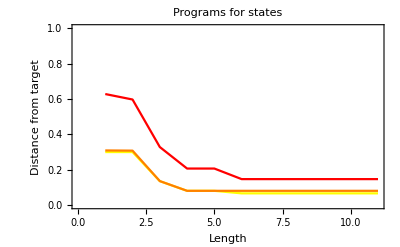

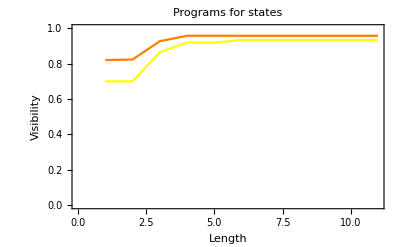

```mathematica
ListLinePlot[{d1,d2,d3},FrameLabel->{"Length","Distance from target"},PlotLabel->HoldForm["Programs for states"],LabelStyle->{GrayLevel[0]}, PlotRange->{{0,11},{0,1}}, Frame-> True, PlotStyle->{Yellow, Orange, Red}]
ListLinePlot[{t1, t2},FrameLabel->{"Length","Visibility"},PlotLabel->HoldForm["Programs for states"],LabelStyle->{GrayLevel[0]}, PlotRange->{{0,11},{0,1}}, Frame-> True, PlotStyle->{Yellow, Orange, Red}]
```

```mathematica
t =Transpose[files][[1]];
dist = Transpose[files][[2]];
target=ToExpression@StringSplit[StringReplace[Transpose[files][[3]], { "["-> "", "]"-> ""}], ", "]
mix=StringSplit[StringReplace[Transpose[files][[4]], { "["-> "", "]"-> ""}], ", "]
output = StringSplit[StringReplace[Transpose[files][[5]], { "["-> "", "]"-> ""}], ", "]
{length, visibility} = Transpose@ToExpression@Table[StringSplit[FileNameTake[outNames[[i]]], "V"], {i, 1, Length@outNames}];
data =Table[{length[[i]], visibility[[i]], files[[i]]}, {i, 1, Length@length}];

means = Table[{length[[i]], visibility[[i]], Mean[files[[i]]]},{i,1,Length@length}];
```

{{0.87338,0.0993619,0.476797},{-0.396473,0.865011,0.307514}}

{{-0.1790718076969229,-7.558912603602892e-12,-1.2585984195263277e-11},{-0.009514576968213949,0.3083268026038142,0.19611867412078585}}

{{0.5296787345141645,0.08063255483481668,0.38692216776003774},{0.2433384467461541,-0.24333844660398898,3.4937765436578095e-11}}

```mathematica
ToExpression[StringSplit[StringReplace[Transpose[files][[3]],{ "["-> "", "]"-> ""}], ", "]]
```

2.87338

```mathematica
firstToEnd[d_]:=AppendTo[d[[2;;]],First@d];
```

```mathematica
ByLength=firstToEnd[firstToEnd[Gather[means, First[#1]==First[#2]&]]]
d =SortBy[Last@ByLength, #[[2]] &]
```

Set::setps: {{{10,0.9,0.335592,1.04884},{10,0.95,0.573449,0.668431},{10,1.,0.957986,0.0655811}},{{11,0.7,0.0190488,1.58712},{11,0.75,0.0407778,1.56207},{11,0.8,0.0827931,1.50873},{11,0.85,0.162587,1.28906},{11,0.9,0.303438,1.09982},{11,1.,0.968607,0.0500997}},{{1,0.9,0.,1.57865},{1,0.95,0.,1.56774},{1,1.,0.,1.56517}},«5»,{{7,0.9,0.439663,0.884202},{7,0.95,0.633342,0.574623},{7,1.,0.908227,0.142901}},{{8,0.9,0.399794,0.947257},{8,0.95,0.610073,0.611065},{8,1.,0.924289,0.118156}},«1»} in the part assignment is not a symbol.

Set::setps: {{{11,0.7,0.0190488,1.58712},{11,0.75,0.0407778,1.56207},{11,0.8,0.0827931,1.50873},{11,0.85,0.162587,1.28906},{11,0.9,0.303438,1.09982},{11,1.,0.968607,0.0500997}},{{1,0.9,0.,1.57865},{1,0.95,0.,1.56774},{1,1.,0.,1.56517}},{{2,0.9,0.148925,1.33945},{2,0.95,0.244577,1.18992},{2,1.,0.278507,1.12954}},«5»,{{8,0.9,0.399794,0.947257},{8,0.95,0.610073,0.611065},{8,1.,0.924289,0.118156}},{{9,0.9,0.36656,0.999925},{9,0.95,0.593563,0.63688},{9,1.,0.941377,0.0917682}},«1»} in the part assignment is not a symbol.

{{{1,0.9,0.,1.57865},{1,0.95,0.,1.56774},{1,1.,0.,1.56517}},{{2,0.9,0.148925,1.33945},{2,0.95,0.244577,1.18992},{2,1.,0.278507,1.12954}},{{3,0.9,0.425794,0.902922},{3,0.95,0.528138,0.742797},{3,1.,0.620659,0.597311}},{{4,0.9,0.476045,0.829565},{4,0.95,0.617605,0.601889},{4,1.,0.762432,0.376436}},{{5,0.9,0.490525,0.806091},{5,0.95,0.641921,0.561748},{5,1.,0.843907,0.246636}},{{6,0.9,0.47863,0.82279},{6,0.95,0.643315,0.559739},{6,1.,0.892704,0.167803}},{{7,0.9,0.439663,0.884202},{7,0.95,0.633342,0.574623},{7,1.,0.908227,0.142901}},{{8,0.9,0.399794,0.947257},{8,0.95,0.610073,0.611065},{8,1.,0.924289,0.118156}},{{9,0.9,0.36656,0.999925},{9,0.95,0.593563,0.63688},{9,1.,0.941377,0.0917682}},{{10,0.9,0.335592,1.04884},{10,0.95,0.573449,0.668431},{10,1.,0.957986,0.0655811}},{{11,0.7,0.0190488,1.58712},{11,0.75,0.0407778,1.56207},{11,0.8,0.0827931,1.50873},{11,0.85,0.162587,1.28906},{11,0.9,0.303438,1.09982},{11,1.,0.968607,0.0500997}}}

{{11,0.7,0.0190488,1.58712},{11,0.75,0.0407778,1.56207},{11,0.8,0.0827931,1.50873},{11,0.85,0.162587,1.28906},{11,0.9,0.303438,1.09982},{11,1.,0.968607,0.0500997}}

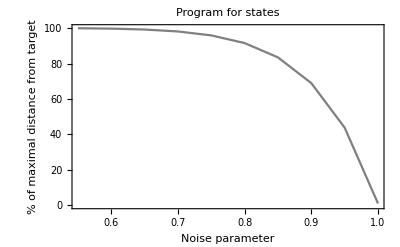

```mathematica
{noiselp, vislp, dislp} =Transpose@d[[All,2;;]] ;
plotlp = ListLinePlot[Transpose@{noiselp, 100 dislp/Max[dislp]},FrameLabel->{"Noise parameter","% of maximal distance from target"},PlotLabel->HoldForm["Program for states"],LabelStyle->{GrayLevel[0]}, PlotRange->{{0.55,1},{0,100}}, Frame-> True, PlotStyle->Gray]
```

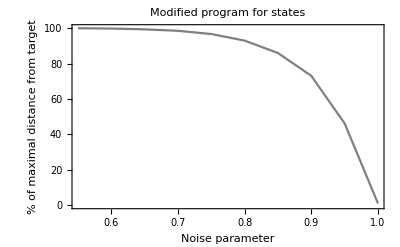

```mathematica
{noiselp2, vislp2, dislp2} =Transpose@d[[All,2;;]] ;
plotlp2 = ListLinePlot[Transpose@{noiselp2, 100 dislp2/Max[dislp2]},FrameLabel->{"Noise parameter","% of maximal distance from target"},PlotLabel->HoldForm["Modified program for states"],LabelStyle->{GrayLevel[0]}, PlotRange->{{0.55,1},{0,100}}, Frame-> True, PlotStyle->Gray]
```

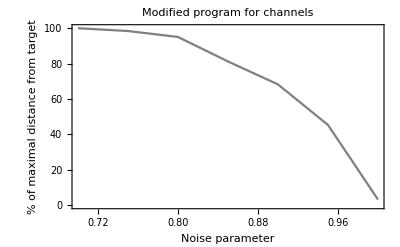

```mathematica
{noiselpch, vislpch, dislpch} =Transpose@d[[All,2;;]] ;
plotlp2 = ListLinePlot[Transpose@{noiselpch, 100 dislpch/Max[dislpch]},FrameLabel->{"Noise parameter","% of maximal distance from target"},PlotLabel->HoldForm["Modified program for channels"],LabelStyle->{GrayLevel[0]}, PlotRange->{{0.7,1},{0,100}}, Frame-> True, PlotStyle->Gray]
```

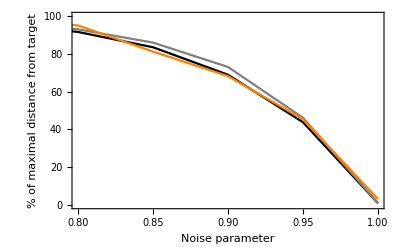

```mathematica
plotcomb = ListLinePlot[{Transpose@{noiselp, 100 dislp/Max[dislp]},Transpose@{noiselp2, 100 dislp2/Max[dislp2]},Transpose@{noiselpch, 100 dislpch/Max[dislpch]}},FrameLabel->{"Noise parameter","% of maximal distance from target"},LabelStyle->{GrayLevel[0]}, PlotRange->{{0.8,1},{0,100}}, Frame-> True, PlotStyle->{Black, Gray, Orange}]
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/distofetacomb.png", plotcomb, "PNG", RasterSize-> 2000]
```

/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/distofetacomb.png

```mathematica
bestT =Table[Transpose[ByLength[[i]]][[3]], {i, 1, Length@ByLength}]
dist=Table[Transpose[ByLength[[i]]][[4]],{i,1,Length@ByLength}];
visibility = Table[Transpose[ByLength[[i]]][[2]], {i, 1, Length@ByLength}];
plotPoints = Table[Transpose@{visibility[[i]], bestT[[i]]}, {i, 1, Length@visibility}]
plots =ListLinePlot[plotPoints, PlotLegends->Placed[{"L = 1", "L =2", "L = 3", "L = 4", "L = 5","L = 6","L = 7","L = 8","L = 9"},{0.6,0.7}], FrameLabel->{"noise parameter", "maximal visibility"},PlotRange->{{0,1},{0,1}}, Frame-> True];
distOfVis=Table[Transpose@{bestT[[i]],dist[[i]]},{i,1,Length@dist}];
plotsDist=ListLinePlot[distOfVis,FrameLabel->{"maximal visibility","distance from target"}, PlotRange->{{0,1},{0,2}}, Frame-> True];
distOfLength = Transpose@Table[Transpose@{i, dist[[i]][[v]]}, {i, 1, Length@dist}, {v, -1, - Length[dist[[1]]], -1}];
ListLinePlot@distOfLength;
```

{{0.,0.,0.},{0.148925,0.244577,0.278507},{0.425794,0.528138,0.620659},{0.476045,0.617605,0.762432},{0.490525,0.641921,0.843907},{0.47863,0.643315,0.892704},{0.439663,0.633342,0.908227},{0.399794,0.610073,0.924289},{0.36656,0.593563,0.941377},{0.335592,0.573449,0.957986},{0.0190488,0.0407778,0.0827931,0.162587,0.303438,0.968607}}

{{{0.9,0.},{0.95,0.},{1.,0.}},{{0.9,0.148925},{0.95,0.244577},{1.,0.278507}},{{0.9,0.425794},{0.95,0.528138},{1.,0.620659}},{{0.9,0.476045},{0.95,0.617605},{1.,0.762432}},{{0.9,0.490525},{0.95,0.641921},{1.,0.843907}},{{0.9,0.47863},{0.95,0.643315},{1.,0.892704}},{{0.9,0.439663},{0.95,0.633342},{1.,0.908227}},{{0.9,0.399794},{0.95,0.610073},{1.,0.924289}},{{0.9,0.36656},{0.95,0.593563},{1.,0.941377}},{{0.9,0.335592},{0.95,0.573449},{1.,0.957986}},{{0.7,0.0190488},{0.75,0.0407778},{0.8,0.0827931},{0.85,0.162587},{0.9,0.303438},{1.,0.968607}}}

{{1,0.},{2,0.278507},{3,0.620659},{4,0.762432},{5,0.843907},{6,0.892704},{7,0.908227},{8,0.924289},{9,0.941377},{10,0.957986},{11,0.968607}}

{{1,0.},{2,0.244577},{3,0.303438},{4,0.528138},{5,0.573449},{6,0.593563},{7,0.610073},{8,0.617605},{9,0.633342},{10,0.641921},{11,0.643315}}

{{1,0.},{2,0.148925},{3,0.162587},{4,0.335592},{5,0.36656},{6,0.399794},{7,0.425794},{8,0.439663},{9,0.476045},{10,0.47863},{11,0.490525}}

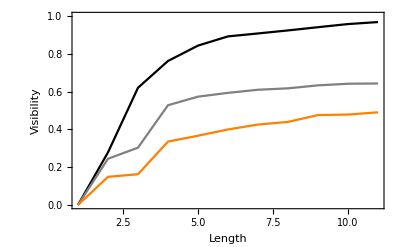

```mathematica
v = -1;
tLpoints1 = Transpose@{Transpose@Table[{i, Last[plotPoints[[i]][[v]]]}, {i, 1, Length@plotPoints}][[All,1]],Sort[Transpose@Table[{i, Last[plotPoints[[i]][[v]]]}, {i, 1, Length@plotPoints}][[All,2]]]}
tLpoints2 = Transpose@{Transpose@Table[{i, Last[plotPoints[[i]][[v-1]]]}, {i, 1, Length@plotPoints}][[All,1]],Sort[Transpose@Table[{i, Last[plotPoints[[i]][[v-1]]]}, {i, 1, Length@plotPoints}][[All,2]]]}
tLpoints3 = Transpose@{Transpose@Table[{i, Last[plotPoints[[i]][[v-2]]]}, {i, 1, Length@plotPoints}][[All,1]],Sort[Transpose@Table[{i, Last[plotPoints[[i]][[v-2]]]}, {i, 1, Length@plotPoints}][[All,2]]]}

tL = Show[ListLinePlot[{tLpoints1,tLpoints2,tLpoints3}, PlotRange->{{1,11},{0,1}}, PlotStyle->{Black,Gray, Orange}],FrameLabel->{"Length","Visibility"},LabelStyle->{GrayLevel[0]}, PlotRange->{{1,11},{0,1}}, Frame-> True]
```

```mathematica
Export["/home/jakub/Dokumenty/UW/III-rok/licencjat/praca/fig/tOfLcomb.png", tL, "PNG", RasterSize-> 2000];
```

```mathematica
tLpoints
```

{{1,0.40338},{2,0.722035},{3,0.760227},{4,0.745791},{5,0.722711},{6,0.70868},{7,0.681466},{8,0.650831},{9,0.619113},{10,0.591254},{11,0.562684}}

```mathematica
1 - 0.91/0.9686
```

0.0604997

```mathematica
target = {{0.59207205,-0.32598238,0.73701165},{-0.74020855,-0.58159546,0.3373989},{0.31865654,-0.74530679,-0.58564136}}
output = {{0.08821138,-0.04856733,0.10980558},{-0.11028188,-0.0866505,0.05026825},{0.04747587,-0.11104145,-0.08725329}}
Norm[ target- output, Infinity]
Norm[target, Infinity]
Norm[output, Infinity]
```

{{0.592072,-0.325982,0.737012},{-0.740209,-0.581595,0.337399},{0.318657,-0.745307,-0.585641}}

{{0.0882114,-0.0485673,0.109806},{-0.110282,-0.0866505,0.0502683},{0.0474759,-0.111041,-0.0872533}}

1.412

1.6592

0.247201

```mathematica
Det[target]
```

1.

```mathematica
t2 = target / Norm[target, Infinity]
Norm[t2, Infinity]
```

{{0.356841,-0.196469,0.444196},{-0.446123,-0.350527,0.20335},{0.192054,-0.449196,-0.352965}}

1.

```mathematica
Norm[t2 - output, Infinity]
```

0.752799